2 x

NDSolve::mxst: Maximum number of 10000 steps reached at the point n == 25.4486.

{{ϕ→InterpolatingFunction[{{25.4486,60.}},<>]}}

InterpolatingFunction::dmval: Input value {0.00122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

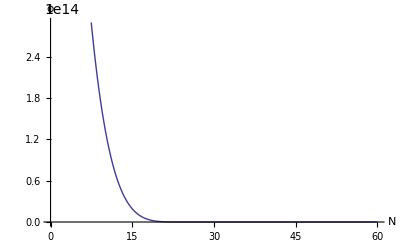

InterpolatingFunction::dmval: Input value {0.00122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

-Graphics-

```mathematica
(* This is necessary for removing previously defined variables *)
ClearAll["Global`*"]
(* Define a potential *)
(*v[x_] := x^4*(1-Log[x])*)
v[x_] := x^2
vp[x_]=v'[x]
findϕ := Module[{h,hsq,nsr,ϕ60,ϕp60},
(* Define H as a function of number of efolds *)
h[n_]:= Simplify[√(v[ϕ[n]]/(3-1/2*ϕ'[n]^2))];
hsq[n_]:=v[ϕ[n]]/(3-1/2*ϕ'[n]^2);
(* Define number of efolds using slow-roll approx *)
nsr[x_] := v[x]/v''[x];(*NEED FACTORS*)
(* find ϕ60, ϕ at n=60 *)
ϕ60 = Evaluate[Last[FindRoot[{nsr[x]-60==0},{x,1}]]];
(* find ϕp60 = ϕ'[60] *)
ϕp60 = v'[x]/v[x]/.ϕ60 ;
(* Solve for ϕ[n] *)NDSolve[{2*hsq[n]*ϕ''[n]+hsq[n]*(ϕ'[n])^3-6*hsq[n]*ϕ'[n]+2*v'[ϕ[n]]==0,ϕ[60]==(x/.ϕ60),ϕ'[60]==ϕp60},ϕ,{n,60,0},InterpolationOrder->All]]
ϕsol = findϕ
Plot[Evaluate[ϕ[n]/.ϕsol],{n,60,0},AxesLabel->{N,ϕ}]
Plot[Evaluate[6-(ϕ'[n])^2/.ϕsol],{n,60,0},AxesLabel->{N,"6-ϕp^2"}]
```

InterpolatingFunction::dmval: Input value {0.00122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

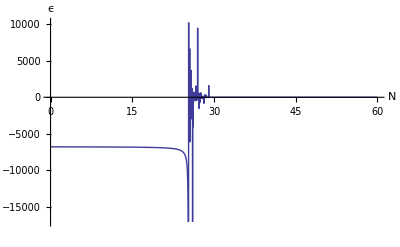

```mathematica
findϵ := Module[{ϵ},
(* Find ϵ[n] *)
ϵ[n_] := 1/2*D[Log[v[ϕ[n]/.ϕsol]],n];
Return[ϵ[n]]]
ϵ[n_] := findϵ 
Plot[Evaluate[ϵ[n]],{n,60,0},AxesLabel->{N,ϵ}]
```

InterpolatingFunction::dmval: Input value {0.00122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

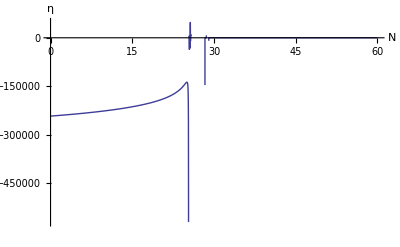

```mathematica
findη := Module[{ϕp,η},
(* Find η[n] *)
ϕp[x_] := v'[x]/v[x];
η[n_] := 1/2*D[Log[vp[ϕ[n]/.ϕsol]]^2,n];
Return[η[n]]]
η[n_] := findη
Plot[Evaluate[η[n]],{n,60,0},AxesLabel->{N,η}]
```

InterpolatingFunction::dmval: Input value {0.00122571} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

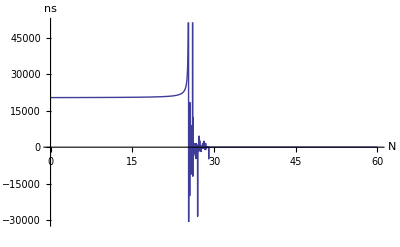

```mathematica
findNs := Module[{ns,ϕ60},
ns[n_] := 1-2*ϵ[n]+D[Log[ϵ[n]],n];
Return[ns[n]]]
ns[n_] := findNs
Plot[Evaluate[ns[n]],{n,60,0},AxesLabel->{N,ns}]
```

{}

NDSolve::mxst: Maximum number of 10000 steps reached at the point n == 25.4486.

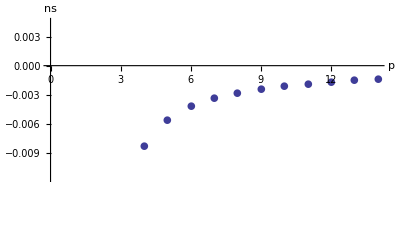

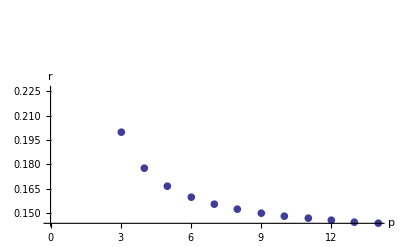

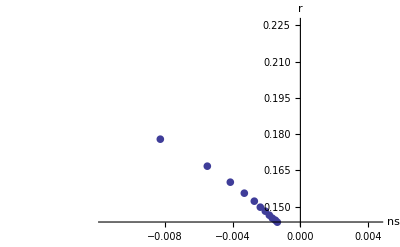

```mathematica
nsList = {}; rList = {};pList = {}
For[p=2,p<15,p++,
v[ϕ_] := ϕ^p;
ϕsol = findϕ;
ns[n_] = Last[findNs];
ϵ[n_] = Last[findϵ ];
AppendTo[nsList,ns[60]];
AppendTo[rList,16*ϵ[60]];
AppendTo[pList,p]]
ListPlot[Thread[{pList,nsList}],AxesLabel->{"p",ns},PlotMarkers->{●,10}]
ListPlot[Thread[{pList,rList}],AxesLabel->{"p",r},PlotMarkers->{●,10}]
ListPlot[Thread[{nsList,rList}],AxesLabel->{ns,r},PlotMarkers->{●,10}]
```